```mathematica
SetDirectory[NotebookDirectory[]];

Needs["ErrorBarPlots`"];
Needs["DatabaseLink`"];

$PlotTheme = "Default";
frameLabelStyle[text_]:= Style[text, FontSize->12,FontColor->Gray];
frameTicksStyle = Directive[FontSize-> 8, FontColor-> Gray];
legendStyle [text_]:= Style[text, FontSize->12, FontColor->Gray];
plotLabelStyle[text_]:= Style[text, FontSize->14, FontColor->Gray];
cm = 72/2.54;
colorMap = 97;

thesisImages = FileNameJoin[{NotebookDirectory[], "..", "..", "thesis","chapters","img"}];

<<"data-helpers.wls";
<<"level-helpers.wls";
<<"train-helpers.wls";
<<"visualise-helpers.wls";
```

## Import Data From Database

```mathematica
conn = OpenSQLConnection[JDBC["PostgreSQL","127.0.0.1/teodor"],"Username"->"teodor"];
```

```mathematica
tracksSimulatedLDManual = readDataOneOfEach[81];
tracksSimulatedLDMC = readDataOneOfEach[82];
```

```mathematica
CloseSQLConnection[conn];
```

## Visualising Data

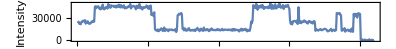
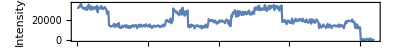
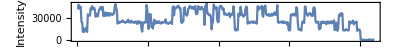
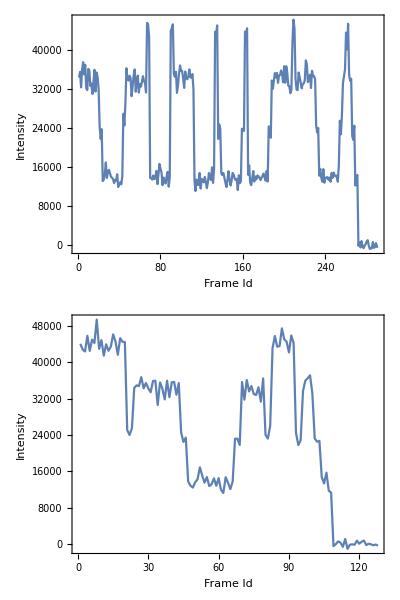

```mathematica
Block[{plot, img1, img2, img3, img4},
plot = ListLinePlot[#[[dataIntI, All, counts]],
AspectRatio->1/8, 
ImageSize->14cm,
PlotRange->All,
Frame-> True,
FrameLabel->(frameLabelStyle/@{"Frame Id", "Intensity"}),
FrameTicksStyle->frameTicksStyle
]&;
img1 = plot@tracksSimulatedLDMC[[1]];
img2 = plot@tracksSimulatedLDMC[[41]];
img3 = plot@tracksSimulatedLDMC[[81]];
img4 = Column[plot/@tracksSimulatedLDManual];
Export[FileNameJoin[{thesisImages, "level-detect-training-set-large-step.pdf"}],img1];
Export[FileNameJoin[{thesisImages, "level-detect-training-set-small-step.pdf"}],img2];
Export[FileNameJoin[{thesisImages, "level-detect-training-set-short-level.pdf"}],img3];
Export[FileNameJoin[{thesisImages, "level-detect-training-set-manual.pdf"}],img4];
Column[{img1, img2,img3, img4}]
]
```

```mathematica
hw = 5;
```

```mathematica
data = labelMC[tracksSimulatedLDMC, hw];
```

```mathematica
evects = Eigenvectors@Covariance@Keys@data;
```

```mathematica
s1=labelMC[{tracksSimulatedLDMC⟦1⟧},hw];
s2=labelMC[{tracksSimulatedLDMC⟦2⟧},hw];
s3=labelMC[{tracksSimulatedLDMC⟦3⟧},hw];
s4=labelMC[{tracksSimulatedLDMC⟦4⟧},hw];
s5=labelMC[{tracksSimulatedLDMC⟦5⟧},hw];
```

```mathematica
indexVisualiseData =1;
```

```mathematica
Row[{Slider[Dynamic@indexVisualiseData, {1, Min[Length@s1, Length@s4], 1}], Button["Next", indexVisualiseData =Min[Length@s1, Length@s4, indexVisualiseData+1]  ]}]
```

```mathematica
ListPointPlot3D[{
Keys[Select[data, Values@#==yes&]].Transpose[evects[[1;;3]] ],
Keys[Select[data, Values@#==no&]].Transpose[evects[[1;;3]] ]
}
]
```

-Graphics3D-

States of simulated tracks are generated by Markov chain. For each Markov chain 9 tracks are generated by adding noise to the fluorophores. Each MC follows a different curve in the high dimensional space. Therefore the tracks in each batch follows the same curve and has small deviations created by the noise.

To train a neural networks properly there needs to be tracks generated by many MCs. Suggestions could be to create many simulations, for example few hundred, and use 1 track from each data set. Then train NN on tracks generated by a variety  of MC and test on new MCs.

```mathematica
Clear[data, hw, evects, s1, s2, s3, s4, indexVisualiseData]
```

## Find Optimal Parameters

The data is extracted by taking hw frames in each direction around each frame, resulting in a vector x ∈ R^(2*hw+1). The these vectors are classified into two categories, which are transitional frame, yes, and not a transitional frame, no. The data is labelled based on the states of the Markov chain used to generate the track.

In this data set the yes  class is the minority class, therefore the performance of the classifier will be measured in terms of F1 score for the positive class.

### Find the best window size

For each window size train neural networks with hidden units starting from 1, ending at 40, with increments of 5. Repeat this experiment 10 times to remove the effects of randomly splitting the data into training and testing.

#### Train neural network

Running the neural network for hidden units from 1 to 100:

```mathematica
hus
```

{1,5,10,15,20,25,30,40,50,60,80,100}

```mathematica
BinarySerialize[
Table[
Print[i, "..."];
Table[Block[{rawtrain, rawtest, m, s, train, test},
{rawtrain, rawtest} = randomTrainTest[tracksSimulatedLDMC, tracksSimulatedLDManual];

m = Mean[Keys[Join[rawtrain, rawtest]]];
s = StandardDeviation[Keys[Join[rawtrain, rawtest]]];

train =whitenData[rawtrain, m, s]; 
test = whitenData[rawtest, m, s];

Print["  ", hw];

nnetTrail[train, test, hus, 1000]
],
{hw, 5, 15, 5}],
{i, 1, 10}]
]>>"result-classify-windowSize-f1Score.bin";
```

Running the neural network for hidden units from 1 to 10 with increment of 1

```mathematica
BinarySerialize[
Table[
Print[i, "..."];
Block[{rawtrain, rawtest, m, s, train, test, hw},
hw = 5;
{rawtrain, rawtest} = randomTrainTest[tracksSimulatedLDMC, tracksSimulatedLDManual];

m = Mean[Keys[Join[rawtrain, rawtest]]];
s = StandardDeviation[Keys[Join[rawtrain, rawtest]]];

train =whitenData[rawtrain, m, s]; 
test = whitenData[rawtest, m, s];


nnetTrail[train, test, Range[1, 10], 1000]
],
{i, 1, 10}]
]>>"result-classify-hu_1_10-f1Score.bin";
```

Running the neural network for hidden units from 11 to 20 with increment of 1

```mathematica
BinarySerialize[
Table[
Print[i, "..."];
Block[{rawtrain, rawtest, m, s, train, test, hw},
hw = 5;
{rawtrain, rawtest} = randomTrainTest[tracksSimulatedLDMC, tracksSimulatedLDManual];

m = Mean[Keys[Join[rawtrain, rawtest]]];
s = StandardDeviation[Keys[Join[rawtrain, rawtest]]];

train =whitenData[rawtrain, m, s]; 
test = whitenData[rawtest, m, s];


nnetTrail[train, test, Range[11, 20], 1000]
],
{i, 1, 10}]
]>>"result-classify-hu_11_20-f1Score.bin";
```

#### Visualise the result.

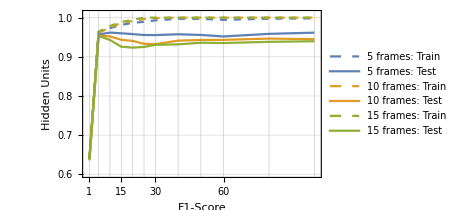

```mathematica
Block[{f1Score, img},
f1Score = BinaryDeserialize[<<"result-classify-windowSize-f1Score.bin"];
img = ListLinePlot[Transpose[{hus, #}]&/@Flatten[Transpose[Mean@f1Score, {1, 3, 2}], 1],
PlotStyle->{Directive[ColorData[colorMap][1], Dashed],
Directive[ColorData[colorMap][1], Thick],
Directive[ColorData[colorMap][2], Dashed],
Directive[ColorData[colorMap][2], Thick],
Directive[ColorData[colorMap][3], Dashed],
Directive[ColorData[colorMap][3], Thick],
Directive[ColorData[colorMap][4], Dashed],
Directive[ColorData[colorMap][4], Thick]},
PlotLegends->Placed[(legendStyle/@{
"5 frames: Train",
"5 frames: Test",
"10 frames: Train",
"10 frames: Test",
"15 frames: Train",
"15 frames: Test",
"20 frames: Train",
"20 frames: Test"
}), Below],
Frame-> True,
PlotRange->{{0,101},{0.6, 1.01}},
GridLines->{hus,Automatic},
FrameTicks-> {{Automatic, None},{hus, None}},
FrameTicksStyle->frameTicksStyle,
FrameLabel->(frameLabelStyle/@{"F1-Score", "Hidden Units"}),
ImageSize->12cm
];
Export[FileNameJoin[{thesisImages, "level-detect-neural-network-result.pdf"}], img];
img
]
```

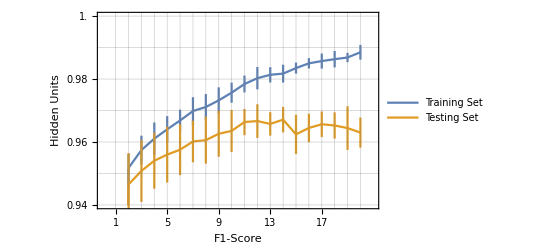
{-Graphics-,{0.623432,0.614491}}

```mathematica
Block[{f1Score, f1Score1,f1Score2, img},
f1Score1 = BinaryDeserialize[<<"result-classify-hu_1_10-f1Score.bin"];
f1Score2 = BinaryDeserialize[<<"result-classify-hu_11_20-f1Score.bin"];
(*Since the experiments for 1 to 10 hidden units and 11 to 20 were ran separately they need to be joined together to be plotted.*)
f1Score = Transpose[Join[Transpose[f1Score1], Transpose[f1Score2]]];
img = ErrorListPlot[
(Transpose[{Transpose[{Range[1, 20], #1}],ErrorBar/@#2}]&@@{Mean@#, StandardDeviation@#}
)&/@Transpose[f1Score, {2, 3, 1}],
Frame-> True,
FrameTicks->{{Range[0.94, 1., 0.01], None}, {Range[1, 20, 1], None}},
PlotRange->{{0, 21}, {0.94, 1.0}},
FrameTicksStyle->frameTicksStyle,
GridLines->{Range[1, 20], Range[0.94, 1.0, 0.010]},
Joined-> True,
FrameLabel->(frameLabelStyle/@{"F1-Score","Hidden Units"}),
PlotLegends->Placed[(legendStyle/@{"Training Set", "Testing Set"}), Below]
];
Export[FileNameJoin[{thesisImages, "level-detect-neural-network-result-n5.pdf"}],img];
{img, Mean[f1Score][[1]]}
]
```

```mathematica
Mean@BinaryDeserialize[<<"result-classify-hu_11_20-f1Score.bin"]
```

{{0.978425,0.966346},{0.980267,0.966654},{0.981358,0.965746},{0.981732,0.967101},{0.983488,0.96243},{0.985,0.964462},{0.985719,0.965636},{0.986319,0.965257},{0.986855,0.964427},{0.988512,0.962997}}

### Try to compress data with PCA and Auto-Encoder

```mathematica
AppendTo[$Path, FileNameJoin[{Directory[], "..", "common"}]];
<<RBM`
```

```mathematica
acTransformGetParams[data_, newMax_, newMin_]:= Block[{oldMax, oldMin,a ,b},
oldMax = Max@data;
oldMin = Min@data;
a = (newMax - newMin)/(oldMax - oldMin);
b = newMin - a*oldMin;
{a, b}
];
acTransform[data_, params_]:= data*params[[1]] + params[[2]];
acRecover[data_, params_]:= (data - params[[2]])/params[[1]];
```

Windows size of 5 was determined to be the best option.

```mathematica
hw = 5;
```

Split the data into training and testing set. The split should be done at level tracks, because the data generated by each track follows specific pattern.

```mathematica
subspaces = {2, 4, 6};
```

Training and testing data sets. These need to be transformed according each algorithm/

```mathematica
{train, test} = randomTrainTest[tracksSimulatedLDMC, tracksSimulatedLDManual];
```

#### Compress via PCA

```mathematica
{evects, evals} = {Eigenvectors@#, Eigenvalues@#}&@Covariance@Keys@train;
```

```mathematica
BinarySerialize[{evects, evals}]>> "compress-hw_5-pca.bin";
```

#### Compress via Auto-Encoder

```mathematica
acTransformParams = acTransformGetParams[Join[Keys@train, Keys@test], 0.95, -0.95];
```

```mathematica
BinarySerialize[acTransformParams]>> "compress-hw_5-autoencoders_params.bin"
```

Train restricted Boltzmann machines.

```mathematica
acEpoch = 1000;
epoch = 1000;
lrate = 0.01;
momentum = 0.9;
```

```mathematica
data = <||>;
rbms = <||>;
ac = <||>;
```

```mathematica
data[11] = acTransform[Keys@train, acTransformParams];
```

```mathematica
rbms[8] = RBMTrain[8, data[11], LearningRate-> lrate, Momentum -> momentum, MaxTrainingRounds-> epoch];
```

```mathematica
data[8] = RBMHiddenExpectation[rbms[8], data[11]];
rbms[6] = RBMTrain[6, data[8], LearningRate-> lrate, Momentum -> momentum, MaxTrainingRounds-> epoch];
```

```mathematica
data[6] = RBMHiddenExpectation[rbms[6], data[8]];
rbms[4] = RBMTrain[4, data[6], LearningRate-> lrate, Momentum -> momentum, MaxTrainingRounds-> epoch];
```

```mathematica
data[4] = RBMHiddenExpectation[rbms[4], data[6]];
rbms[2] = RBMTrain[2, data[4], LearningRate-> lrate, Momentum -> momentum, MaxTrainingRounds-> epoch];
```

```mathematica
Dynamic@ListLinePlot[
Global`errors,
GridLines->Automatic,
Frame-> True]
```

```mathematica
BinarySerialize[rbms]>>"compress-hw_5-rbms.bin"
```

```mathematica
ac[6] = NetChain[RBMAutoEncoder[{rbms[8], rbms[6]}], "Input" -> 11];
ac[4] = NetChain[RBMAutoEncoder[{rbms[8], rbms[6], rbms[4]}], "Input" -> 11];
ac[2] = NetChain[RBMAutoEncoder[{rbms[8], rbms[6], rbms[4], rbms[2]}], "Input" -> 11];
```

```mathematica
BinarySerialize[ac]>>"compress-hw_5-autoencoders_untrained.bin";
```

Train the auto-encoders using ADAM algorithm.

```mathematica
tdata=(#1->#2&)@@@Transpose[{data[11],data[11]}];
```

```mathematica
tac = <||>;
```

```mathematica
tac[6] = NetTrain[ac[6],
tdata,
Method-> "ADAM",
LossFunction->MeanSquaredLossLayer[],
MaxTrainingRounds->acEpoch];
```

```mathematica
tac[4] = NetTrain[ac[4],
tdata,
Method-> "ADAM",
LossFunction->MeanSquaredLossLayer[],
MaxTrainingRounds->acEpoch];
```

```mathematica
tac[2] = NetTrain[ac[2],
tdata,
Method-> "ADAM",
LossFunction->MeanSquaredLossLayer[],
MaxTrainingRounds->acEpoch];
```

```mathematica
BinarySerialize[tac]>>"compress-hw_5-autoencoders_trained.bin";
```

#### Results

```mathematica
tac = BinaryDeserialize[<<"compress-hw_5-autoencoders_trained.bin"];
ac = BinaryDeserialize[<<"compress-hw_5-autoencoders_untrained.bin"];
{evects, evals} = BinaryDeserialize[<<"compress-hw_5-pca.bin"];
acTransformParams = BinaryDeserialize[<<"compress-hw_5-autoencoders_params.bin"];
```

```mathematica
measurePCAError[data_, evects_]:=
Mean[(#.#&/@(data - data.Transpose[evects⟦1;;#1⟧].evects⟦1;;#1⟧))]&/@subspaces
measureACError[data_, ac_, params_]:=
Function[subspace, Mean[ParallelMap[
(#.#&@(acRecover[#,params] - acRecover[ac[subspace][#] , params]))&,
acTransform[data, params]
]]]/@subspaces
```

```mathematica
result = 
Transpose[{subspaces, #}]&/@{
measurePCAError[Keys@train, evects],
measurePCAError[Keys@test, evects],
measureACError[Keys[train],tac, acTransformParams],
measureACError[Keys[test],tac, acTransformParams],
measureACError[Keys[train],ac, acTransformParams],
measureACError[Keys[test],ac, acTransformParams]
};
```

```mathematica
BinarySerialize[result]>>"result-compress-squared_diff.bin"
```

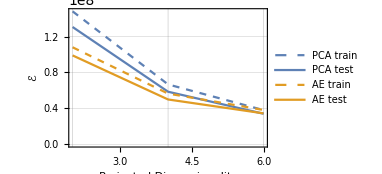

```mathematica
Block[{img},
img = Show[
ListLinePlot[result[[1;;-3]],
PlotStyle->{
Directive[ColorData[colorMap][1], Dashed],
Directive[ColorData[colorMap][1], Thick],
Directive[ColorData[colorMap][2], Dashed],
Directive[ColorData[colorMap][2], Thick],
Directive[ColorData[colorMap][3], Dashed],
Directive[ColorData[colorMap][3], Thick]
},
Frame-> True,
FrameLabel->(frameLabelStyle/@{"Projected Dimensionality","ℰ"}),
FrameTicksStyle->frameTicksStyle,
GridLines->{{2,4, 6},Automatic},
PlotLegends->(legendStyle/@{
"PCA train",
"PCA test",

"AE train",
"AE test",

"Untrained AC train",
"Untrained AC test"
}),
ImageSize-> 10cm
]
];
Export[FileNameJoin[{thesisImages, "level-detect-neural-network-compression.pdf"}], img];
img
]
```

```mathematica
Clear[train, test, measurePCAError, subspaces,acEpoch, epoch, lrate, momentum, data, rbms, ac, tdata];
```

### Compare Classifier Performance on Compressed and Raw Data

#### Train Network

```mathematica
{train, test} = randomTrainTest[tracksSimulatedLDMC, tracksSimulatedLDManual];
```

```mathematica
hw = 5;
subspaces = {2, 4, 6};
tac = BinaryDeserialize[<<"compress-hw_5-autoencoders_trained.bin"];
ac = BinaryDeserialize[<<"compress-hw_5-autoencoders_untrained.bin"];
{evects, evals} = BinaryDeserialize[<<"compress-hw_5-pca.bin"];
acTransformParams = BinaryDeserialize[<<"compress-hw_5-autoencoders_params.bin"];
```

```mathematica
compress[data_, evects_, ac_, acParams_,subspace_]:=Block[{encoder},
encoder = NetTake[ac[subspace], Length[ac[subspace]]/2];
{
 #1->#2&@@@Transpose[{Keys@data.Transpose@evects[[1;;subspace]], Values@data}],
#1-> #2&@@@Transpose[{encoder/@acTransform[Keys@data, acParams], Values@data}]
}
]
```

```mathematica
BinarySerialize[
Table[
Print[i];
Table[
Block[{
trainRaw, testRaw,
trainPCARaw,trainACRaw, testPCARaw, testACRaw,
trainPCAWhitened, trainACWhitened, testPCAWhitened, testACWhitened,
acM,acSD, pcaM, pcaSD,
res,
hw = 5},
(* Split data into training and testing set *)
{trainRaw, testRaw} = randomTrainTest[tracksSimulatedLDMC, tracksSimulatedLDManual];

(* Project data to lower dimensionality *)
{trainPCARaw, trainACRaw} =compress[trainRaw,evects,tac,acTransformParams, subspace];
{testPCARaw, testACRaw} =compress[testRaw,evects,tac,acTransformParams, subspace];

(* Whiten the data *)
acM = Mean[Join[Keys@trainACRaw, Keys@testACRaw]];
acSD = StandardDeviation[Join[Keys@trainACRaw, Keys@testACRaw]];
trainACWhitened = whitenData[trainACRaw, acM, acSD];
testACWhitened = whitenData[testACRaw, acM, acSD];

pcaM = Mean[Join[Keys@trainPCARaw, Keys@testPCARaw]];
pcaSD = StandardDeviation[Join[Keys@trainPCARaw, Keys@testPCARaw]];
trainPCAWhitened = whitenData[trainPCARaw, pcaM, pcaSD];
testPCAWhitened = whitenData[testPCARaw, pcaM, pcaSD];

Print["subspace ",subspace];
res = {
nnetTrail[trainPCAWhitened, testPCAWhitened, Range[1, 20,2], 1000],
nnetTrail[trainACWhitened, testACWhitened, Range[1, 20,2], 1000]
};
Print[res];
res
],
{subspace, subspaces}],
{i, 1, 10}]
] >> "result-classify-windowSize-compressed-f1Score.bin";
```

#### Result

```mathematica
resCompress= BinaryDeserialize[<<"result-classify-windowSize-compressed-f1Score.bin"];
```

```mathematica
resRaw10= BinaryDeserialize[<<"result-classify-hu_1_10-f1Score.bin"];
resRaw20= BinaryDeserialize[<<"result-classify-hu_11_20-f1Score.bin"];
```

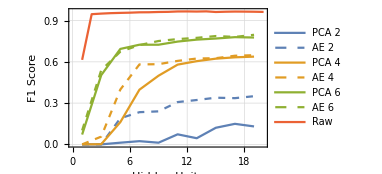

```mathematica
Block[{img},
img = ListLinePlot[
Join[
Transpose[{Range[1, 20, 2], #}]&/@Mean[resCompress]⟦1,All,All,2⟧,
Transpose[{Range[1, 20, 2], #}]&/@Mean[resCompress]⟦2,All,All,2⟧,
Transpose[{Range[1, 20, 2], #}]&/@Mean[resCompress]⟦3,All,All,2⟧,
{Transpose[{Range[1, 20], #}]&@Flatten[{Mean[resRaw10][[All,2]], Mean[resRaw20][[All,2]]}, 1] }
],
Frame -> True,
FrameTicks->Automatic,
FrameTicksStyle->frameTicksStyle,
FrameLabel-> (frameLabelStyle/@{"Hidden Units", "F1 Score"}),
GridLines->Automatic,
PlotLegends->(legendStyle/@{
"PCA 2",
"AE 2",
"PCA 4",
"AE 4",
"PCA 6",
"AE 6",
"Raw"
}),
PlotStyle->{
Directive[{ColorData[colorMap][1]}],
Directive[{ColorData[colorMap][1], Dashed}],

Directive[{ColorData[colorMap][2]}],
Directive[{ColorData[colorMap][2], Dashed}],

Directive[{ColorData[colorMap][3]}],
Directive[{ColorData[colorMap][3], Dashed}],

Directive[{ColorData[colorMap][4]}]
},
ImageSize -> 10cm
];
Export[FileNameJoin[{thesisImages, "level-detect-neural-network-compress-f1score.pdf"}], img];
img
]
```

## Train And Export Neural Network

### Train Neural Network

```mathematica
hw  = 5;
```

```mathematica
{rawTrain, rawTest} = randomTrainTest[tracksSimulatedLDMC, tracksSimulatedLDManual];
```

```mathematica
m = Mean@Keys@Join[rawTrain, rawTest];
s = StandardDeviation@Keys@Join[rawTrain, rawTest];
```

```mathematica
train = (#1-m)/s -> #2 &@@@ Transpose[{Keys@rawTrain, Values@rawTrain}];
test = (#1-m)/s -> #2 &@@@ Transpose[{Keys@rawTest, Values@rawTest}];
```

```mathematica
trained = NetTrain[ 
NetInitialize[
NetChain[{LinearLayer[11], Tanh, LinearLayer[2], SoftmaxLayer[]},
"Input" -> Length@Keys@First@train,
"Output"-> NetDecoder[{"Class", {yes, no}}]
],
Method->{"Xavier", "FactorType"-> "Mean", "Distribution"-> "Normal"}],
train,
Method->"ADAM",
LossFunction->CrossEntropyLossLayer["Index"],
MaxTrainingRounds->2000,
TargetDevice->"CPU"];
```

```mathematica
{
ClassifierMeasurements[#, train, "F1Score"][yes], 
ClassifierMeasurements[#, test, "F1Score"][yes]
} &@ trained
```

{0.974419,0.970634}

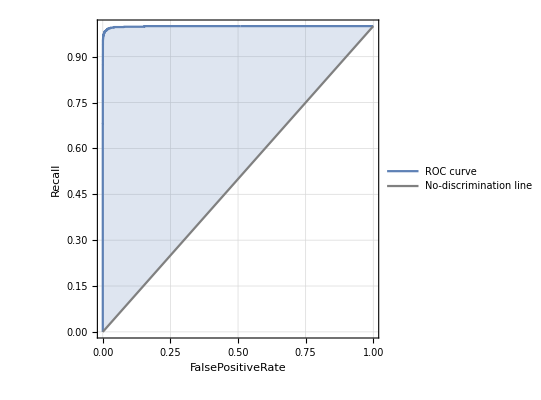

```mathematica
ClassifierMeasurements[#, test, "ROCCurve"][yes]&@trained
```

```mathematica
S = DiagonalMatrix[1/s];
W = NetExtract[trained, {1, "Weights"}];
b = NetExtract[trained, {1, "Biases"}];
```

```mathematica
wtrained = NetJoin[
NetChain[{
LinearLayer[11, "Weights"-> W.S,
	"Biases" ->  b - W.S.m]
}],
NetDrop[trained,1]
];
```

```mathematica
trained[Keys@train[[1]], "Probabilities"]
```

<|yes→0.0120124,no→0.987988|>

```mathematica
wtrained[Keys@rawTrain[[1]], "Probabilities"]
```

<|yes→0.0120125,no→0.987987|>

```mathematica
BinarySerialize[trained] >> "final-network.bin";
BinarySerialize[wtrained] >> "final-network-whitened.bin";
```

### Find Good Bias

```mathematica
ratioResult = {#1[yes]/#1[no]&@wtrained[Keys@#, "Probabilities"], Values[#]}&/@ rawTest;
```

```mathematica
labelResult = {If[#1>0.01, yes, no], #2}&@@@ratioResult;
```

```mathematica
TP = Count[labelResult, {yes, yes}];
FP = Count[labelResult, {yes, no}];
TN = Count[labelResult, {no, no}];
FN = Count[labelResult, {no, yes}];
```

```mathematica
recall = N@TP/(TP + FN);
```

```mathematica
fpr =N@ FP/(FP + TN);
```

```mathematica
{fpr, recall}
```

{0.036926,0.994465}

### Export Trained Network

```mathematica
wtrained = BinaryDeserialize[<<"final-network-whitened.bin"];
```

```mathematica
trained = BinaryDeserialize[<<"final-network.bin"];
```

```mathematica
wtrained[Keys@rawTrain[[2]], "Probabilities"]
```

<|yes→9.64214×10^-7,no→0.999999|>

```mathematica
trained[Keys@train[[2]], "Probabilities"]
```

<|yes→9.64221×10^-7,no→0.999999|>

```mathematica
Export["level-detection-net.h5",{
"Datasets"-> {
"/layer 0/weights" -> NetExtract[wtrained, {1, "Weights"}],
"/layer 0/biases" -> NetExtract[wtrained, {1, "Biases"}],
"/layer 1/weights" -> NetExtract[wtrained, {3, "Weights"}],
"/layer 1/biases" -> NetExtract[wtrained, {3, "Biases"}]
},
"Attributes"-> {
"/layer 0/weights" -> {"Activation" -> "tanh"},
"/layer 1/weights" -> {"Activation" -> "linear"},
"/layer 1/weights" -> {"output" -> "yes = 1 > 2"},
"/layer 1/weights" -> {"threshold" -> "0.01"}
}
},"Rules"]
```

level-detection-net.h5

## Compare 3 Level Detection Algorithms

```mathematica
conn = OpenSQLConnection[JDBC["PostgreSQL","127.0.0.1/teodor"],"Username"->"teodor"];
```

```mathematica
tracksVerify = readDataSet[123];
```

```mathematica
CloseSQLConnection[conn];
```

### Compare Level Detection Algorithms Accuracy

```mathematica
result = {calcAcc[#, #[[levelsI]] ]&/@tracksVerify,
calcAcc[#, #[[levelsOldI]]]&/@tracksVerify,
calcAcc[#, #[[levelsNewI]] ]&/@tracksVerify
};
```

```mathematica
Mean/@result[[All, All, 1]]
```

{1396.22,235.381,180.617}

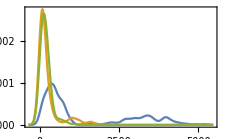

```mathematica
Block[{img},
img =SmoothHistogram[
result[[All, All, 1]],{100,"Gaussian"},
PlotRange->All,
Frame-> True,
FrameTicksStyle-> frameTicksStyle,
ImageSize->8cm,
PlotStyle->(ColorData[colorMap]/@ Range[1, 3]),
PlotLegends->(legendStyle/@{"Level Noise","Bayesian", "Neural Network"}),
Axes->{True, False}
];
Export[FileNameJoin[{thesisImages, "level-detect-compare-E1.pdf"}], img];
img
]
```

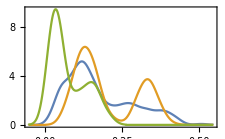

```mathematica
Block[{img},
img = SmoothHistogram[
result[[All, All, 2]],{0.02, "Gaussian"},
PlotRange->All,
Frame-> True,
FrameTicksStyle-> frameTicksStyle,
ImageSize->8cm,
PlotStyle->(ColorData[colorMap]/@ Range[1, 3]),
PlotLegends->(legendStyle/@{"Level Noise","Bayesian", "Neural Network"}),
Axes-> {True, False}
];
Export[FileNameJoin[{thesisImages, "level-detect-compare-E2.pdf"}], img];
img]
```

## Compare 3 Level Detection Algorithms Real Data

### Selecting tracks to test

```mathematica
conn = OpenSQLConnection[JDBC["PostgreSQL","127.0.0.1/teodor"],"Username"->"teodor"];
```

```mathematica
tracksSelected = unpackDBData@@@SQLExecute[conn, "select 
source_data_set, 
source_track_id,
track_size,
frame_dim_int, 
levels, 
levels_old,
levels_new,
data_int 

from smidata
where 
    dataset_id = 13
and category = 1
order by source_data_set, source_track_id"
];
```

```mathematica
CloseSQLConnection[conn];
```

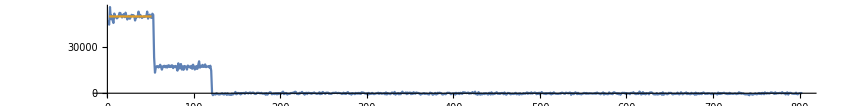

```mathematica
plotTrackLevels[tracksSelected[[1, levelsI]], tracksSelected[[1]]]
```

```mathematica
tracksToUse = {};
index = 1;

Column[
{Dynamic[
ListLinePlot[tracksSelected[[#, dataIntI, All, 2]], PlotRange->All, AspectRatio->1/8, ImageSize->900]&@index
],
Row[{
Button["Previous", index = Max[index-1, 1] ],
Button["Next",index = Min[index+1,Length[tracksSelected] ]], 
Button["Add", tracksToUse = Union[Append[tracksToUse ,{tracksSelected[[index, datasetNameI]],tracksSelected[[index, trackIdI]],1,-1,-1 }]]]
}]
}
]
```

```mathematica
Dynamic@Length@tracksToUse
```

```mathematica
Export["real-verify.csv",tracksToUse]
```

### Selecting Levels

```mathematica
conn = OpenSQLConnection[JDBC["PostgreSQL","127.0.0.1/teodor"],"Username"->"teodor"];
```

```mathematica
tracksRealData = readDataSet[131];
```

```mathematica
CloseSQLConnection[conn];
```

```mathematica
index =96;
```

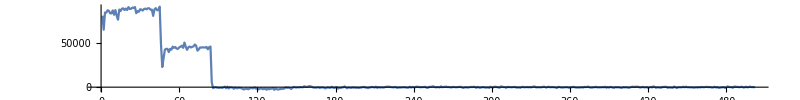

```mathematica
ListLinePlot[tracksRealData[[index,dataIntI,All, 2]] , PlotRange->All, AspectRatio->1/8, ImageSize->800]
```

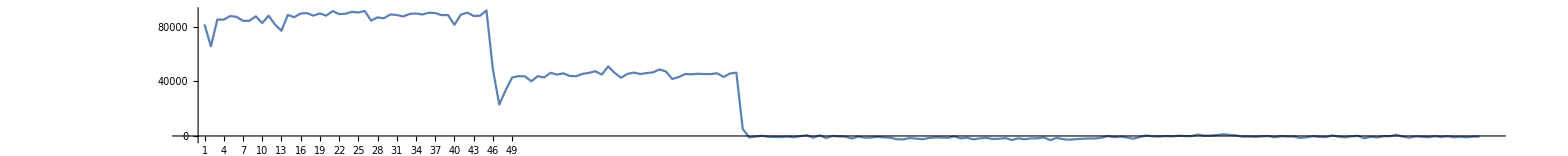

```mathematica
ListLinePlot[tracksRealData[[index,dataIntI,1;;200, 2]] , PlotRange->All, AspectRatio->1/10, ImageSize->5000,
Ticks -> {Range[1, 200, 1], Automatic},
TicksStyle-> Directive[FontSize-> 7, FontColor-> Gray],
GridLines->{Range[1, 200, 1]}]
```

```mathematica
tracksLevels =BinaryDeserialize[<<"level-detection-real-verify-levels.bin"];
```

```mathematica
tracksLevels[tracksRealData[[index, {1,2}]]] = {{1,45},{49, 84}};
```

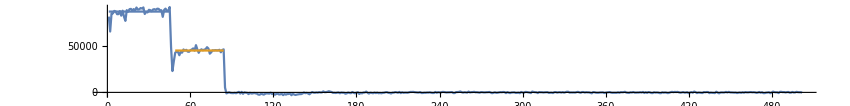

```mathematica
plotTrackLevels[{#}&/@tracksLevels[{tracksRealData[[index, 1]], tracksRealData[[index, 2]]}], tracksRealData[[index]]]
```

```mathematica
BinarySerialize[tracksLevels]>>"level-detection-real-verify-levels.bin";
```

### Compare Algorithms

```mathematica
conn = OpenSQLConnection[JDBC["PostgreSQL","127.0.0.1/teodor"],"Username"->"teodor"];
tracksRealData = readDataSet[131];
CloseSQLConnection[conn];
```

```mathematica
manualLvl = BinaryDeserialize[<<"level-detection-real-verify-levels.bin"];
track = tracksRealData[[2]];
lvls = track[[levelsNewI]];
```

```mathematica
res ={
calcAcc[#, #[[levelsI]],segmentsToLevels[manualLvl[#[[{1, 2}]]] ,#] ],
calcAcc[#, #[[levelsOldI]],segmentsToLevels[manualLvl[#[[{1, 2}]]], #]],
calcAcc[#, #[[levelsNewI]],segmentsToLevels[manualLvl[#[[{1, 2}]]],#] ]
}&/@tracksRealData;
```

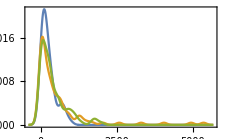

```mathematica
Block[{img},
img = SmoothHistogram[Transpose@res[[All, All, 1]],{100, "Gaussian"},
PlotRange-> {Full,Full},
Frame-> True,
FrameTicksStyle-> frameTicksStyle,
ImageSize->8cm,
PlotStyle->(ColorData[colorMap]/@ Range[1, 3]),
PlotLegends->(legendStyle/@{"Level Noise","Bayesian", "Neural Network"}),
Axes-> {True, False}
];
Export[FileNameJoin[{thesisImages, "level-detect-compare-E1-real.pdf"}], img];
img]
```

```mathematica
Mean[res]
```

{{244.542,0.12212},{555.704,0.0260548},{389.913,0.0967894}}

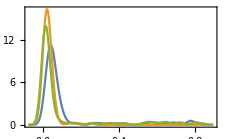

```mathematica
Block[{img},
img= SmoothHistogram[Transpose@res[[All, All, 2]],{0.02, "Gaussian"},
PlotRange->{Full,Full},
Frame-> True,
FrameTicksStyle-> frameTicksStyle,
ImageSize->8cm,
PlotStyle->(ColorData[colorMap]/@ Range[1, 3]),
PlotLegends->(legendStyle/@{"Level Noise","Bayesian", "Neural Network"}),
Axes-> {True, False}
];
Export[FileNameJoin[{thesisImages, "level-detect-compare-E2-real.pdf"}], img];
img]
```

```mathematica
Mean/@Transpose@res[[All, All, 2]]
```

{0.12212,0.0260548,0.0967894}

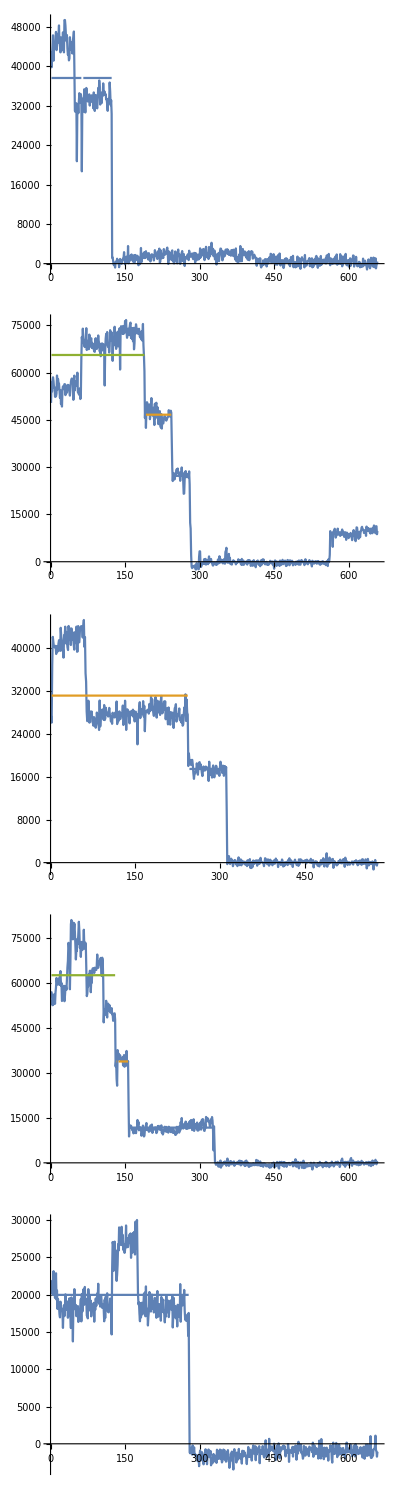

```mathematica
Block[{img},
img = Column[
Function[{val},
plotTrackLevels[#[[levelsOldI]], #, 15cm]&@tracksRealData[[First@Flatten@Position[#,val]&@res[[All, 2, 1]]]]
]/@((Reverse@ Sort@res[[All, 2, 1]])[[1;;5]])
];
Export[FileNameJoin[{thesisImages, "level-detect-old-errors.pdf"}], img];
img
]
```

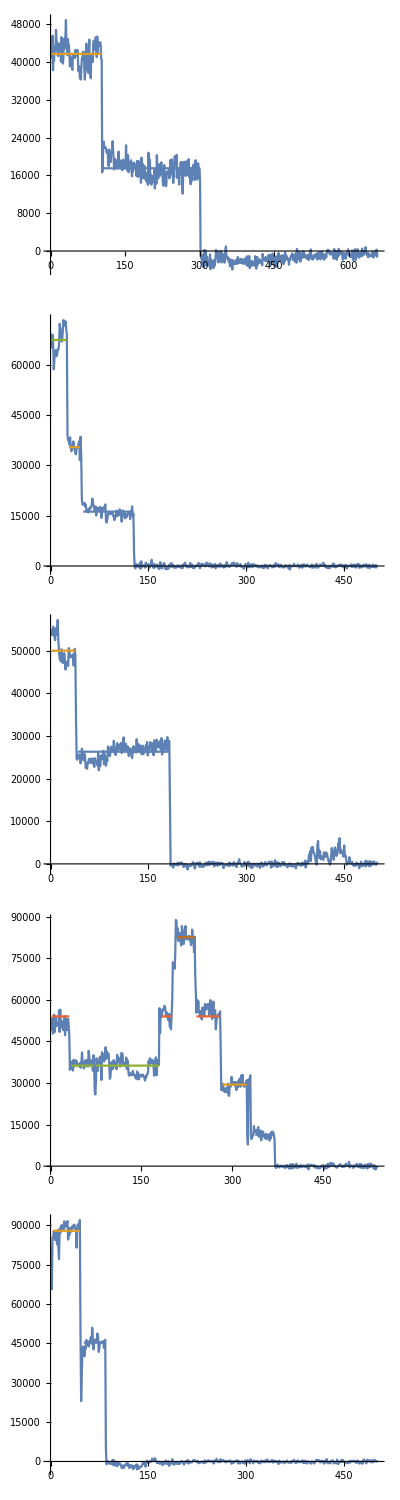

```mathematica
Block[{img},
img = Column[
Function[{val},
plotTrackLevels[#[[levelsOldI]], #, 15cm]&@tracksRealData[[First@Flatten@Position[#,val]&@res[[All, 1, 1]]]]
]/@((Reverse@ Sort@res[[All, 1, 1]])[[1;;5]])
];
Export[FileNameJoin[{thesisImages, "level-detect-viva-errors.pdf"}], img];
img
]
```

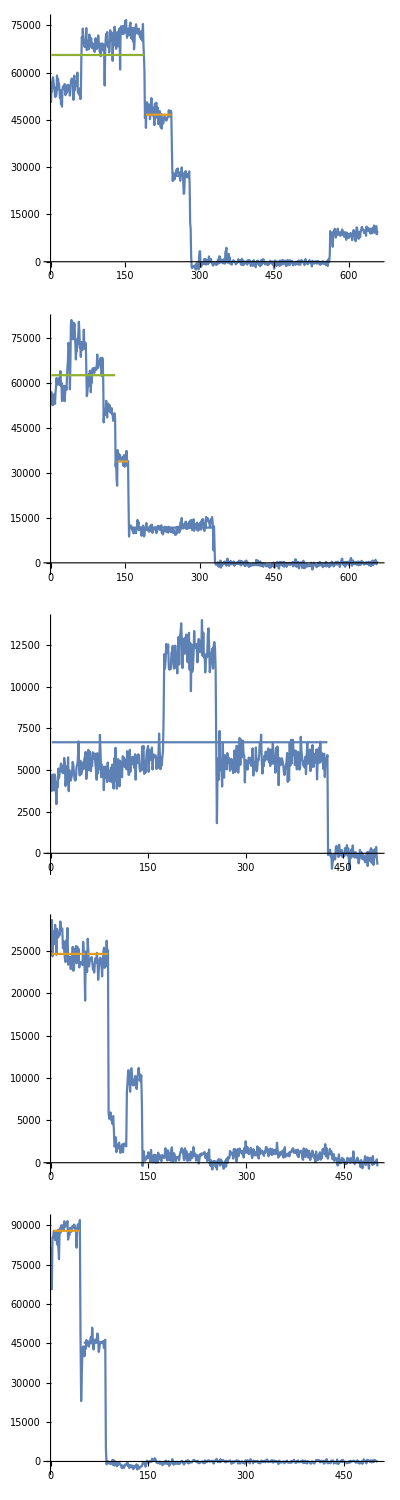

```mathematica
Block[{img},
img = 
Column[
Function[{val},
plotTrackLevels[#[[levelsOldI]], #, 15cm]&@tracksRealData[[First@Flatten@Position[#,val]&@res[[All, 3, 1]]]]
]/@((Reverse@ Sort@res[[All, 3, 1]])[[1;;5]])
];
Export[FileNameJoin[{thesisImages, "level-detect-new-errors.pdf"}], img];
img
]
```